# Notebook 10: Sound and Music

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Representing and playing notes

In Mathematica, you can refer to a named note using the SoundNote command with a string argument. This is how you write Middle C. Note that the SoundNote command doesn’t make a sound by itself.

```mathematica
SoundNote["C"]
```

SoundNote[C]

If you want to give the user an interface for playing notes, use Sound.

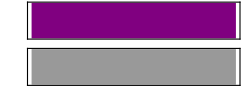

```mathematica
Sound[SoundNote["C"]]
```

A sequence of notes is represented by a list of SoundNote commands.

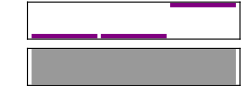

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["G"]}]
```

### Chords

A chord (two or more notes played at the same time) is represented by giving SoundNote a list

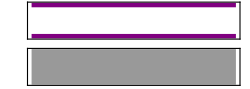

```mathematica
Sound[{SoundNote[{"C","G"}]}]
```

You can specify absolute times, with an overlap, like this

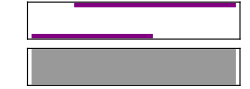

```mathematica
Sound[{SoundNote["C",{0,0.3}],SoundNote["G",{0.1,0.5}]}]
```

A chord of C, E, G and Bb

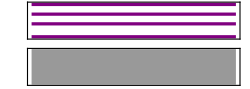

```mathematica
Sound[SoundNote[{"C","E","G","Bb"}]]
```

### Duration

By default, a note is played for 1 second. You can give SoundNote a second argument which is the duration of a note in seconds. Here is how you play Middle C for 1/5th of a second.

```mathematica
Sound[SoundNote["C",.2]]
```

-Graphics-

You can specify a rest with None

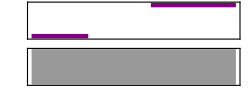

```mathematica
Sound[{SoundNote["C",0.2],SoundNote[None,0.2],SoundNote["G",0.3]}]
```

### Instrument

The default instrument is a piano. You can give SoundNote a third argument, a string, to choose another instrument.

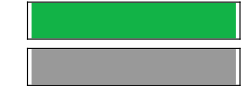

```mathematica
Sound[SoundNote["C",1.5,"Tuba"]]
```

The help file for SoundNote has a complete listing of instruments.

## Describing notes with numbers

You can also describe notes with numbers. Middle C is 0. Each semitone up is counted as +1, and each semitone down is counted as -1. There are 12 semitones in an octave.

```mathematica
Grid[{{"C",12},{"B",11},{"A# Bb",10},{"A",9},{"G# Ab",8},{"G",7},{"F# Gb",6},{"F",5},{"E",4},{"D# Eb",3},{"D",2},{"C# Db", 1}, {"C", 0}},Frame->All]
```

C | 12
B | 11
A# Bb | 10
A | 9
G# Ab | 8
G | 7
F# Gb | 6
F | 5
E | 4
D# Eb | 3
D | 2
C# Db | 1
C | 0

Here is a how you would play Middle G with numbers

```mathematica
Sound[SoundNote[7]]
```

-Graphics-

Here we use Table to generate all of the notes between Middle C and the C one octave up. Each note is one quarter of a second.

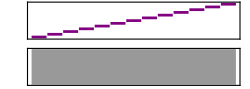

```mathematica
Sound[Table[SoundNote[s,.25],{s,0,12}]]
```

A piano scale usually consists of a mixture of whole steps (i.e., two semitones) and half steps (one semitone). The C blues scale, for example, is C - Eb - F - Gb - Bb - C. Here we use a version of the Table command to play the C blues scale.

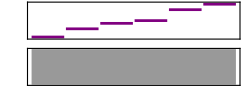

```mathematica
Sound[Table[SoundNote[s,.25],{s,{0,3,5,6,10,12}}]]
```

### Random music

We can use RandomChoice to select a note from a particular scale. This lets us create random music that sounds like it could have been improvised (very poorly).

```mathematica
cBluesScale={0,3,5,6,10,12};
```

```mathematica
RandomChoice[cBluesScale]
```

0

Twenty random notes

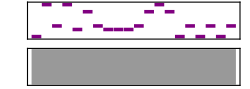

```mathematica
Sound[Table[SoundNote[RandomChoice[cBluesScale],.2],20]]
```

Add possibility of chords. The If statement generates a random real number between 0 and 1. Thirty percent of the time it returns “None” which is silent. Seventy percent of the time it returns another note selected randomly from the same scale.

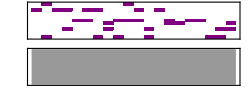

```mathematica
Sound[Table[SoundNote[{RandomChoice[cBluesScale],If[RandomReal[]>.3,RandomChoice[cBluesScale],None]},.2],20]]
```

## Playing percussion

Since percussion instruments are typically not (strongly) pitched, you specify the notes without a pitch.

```mathematica
Sound[SoundNote["Snare"]]
```

-Graphics-

Cowbell sounded every beat

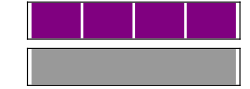

```mathematica
Sound[{SoundNote["Cowbell",{0,0.25}],SoundNote["Cowbell",{0.25,0.5}],SoundNote["Cowbell",{0.5,0.75}],SoundNote["Cowbell",{0.75,1}]}]
```

Add tom drum on the off beat

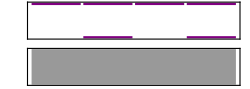

```mathematica
Sound[{SoundNote["Cowbell",{0,0.25}],SoundNote["Cowbell",{0.25,0.5}],SoundNote["LowFloorTom",{0.25,0.5}],SoundNote["Cowbell",{0.5,0.75}],SoundNote["Cowbell",{0.75,1}],SoundNote["LowFloorTom",{0.75,1}]}]
```

Loop to create longer sequence

```mathematica
beat={SoundNote["Cowbell",{0,0.25}],SoundNote["Cowbell",{0.25,0.5}],(*SoundNote["LowFloorTom",{0.25,0.5}],*)SoundNote["Cowbell",{0.5,0.75}],SoundNote["Cowbell",{0.75,1}],SoundNote["LowFloorTom",{0.75,1}]};
```

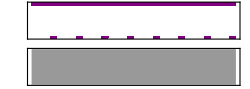

```mathematica
Sound[Table[beat,{8}]]
```

### Importing MIDI files

You can import MIDI files with the Import command. Here is a backbeat from Wikipedia

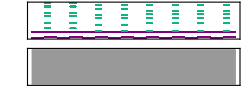

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/b/b6/Backbeat_chop.mid"]
```

## Playing samples and functions

Mathematica has a number of sound samples built in. These open automatically in a player.

```mathematica
ExampleData["Sound"]
```

{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,BlackcapWarbler},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,JetSound},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,OrganChord},{Sound,Piano},{Sound,PianoScale},{Sound,RollingCoin},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,SubwayTrain},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}}

```mathematica
ExampleData[{"Sound","Apollo13Problem"}]
```

-Graphics-

You can Import audio clips in WAV, AIFF and other formats (usually not MP3). Here is the “insert a coin” sound from Donkey Kong

```mathematica
Import["http://www.basementarcade.com/arcade/sounds/DK/insert.wav"]
```

### Playing amplitudes

Mathematica also allows you to treat a sequence of numbers as amplitudes in an audio file. If you give ListPlay a long list of random amplitudes (5000 elements in this case) you can generate a short noise segment

```mathematica
ListPlay[RandomReal[1,{5000}]]
```

-Graphics-

You can use the Play command with a function to generate a pure tone instead. This plays Middle A for 1 second.

```mathematica
Play[Sin[440 2Pi t],{t,0,1}]
```

-Graphics-

## Setting moving images to music

Using EmitSound, it is possible to add sound or music to animations. Here is a version that uses Manipulate

```mathematica
EmitSound[Sound[SoundNote[2]]]
```

```mathematica
Manipulate[EmitSound[Sound[SoundNote[x]]];Graphics[{LightBlue,Rectangle[{0,0},{10,10}],Red,Disk[{x,x}]}],{x,2,8,1}]
```

## In-Class Activity

### Try making a musical composition or setting some moving graphic images to sound.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course